## H_5^+ DVR Initial

## Average Field (Adiabatic Treatment)

### Load Package

```mathematica
Get@"~/Documents/UW/Research/H5+/Common/H5Core.m"
<<ChemTools`DVR`
<<ChemTools`Wavefunctions`
<<ChemTools`DataStructures`
<<ChemTools`Spectroscopy`
```

### Get Wfns

#### KE

```mathematica
$H5DVR["KineticEnergy"]//MatrixPlot
```

-Graphics-

#### PE

##### Mat PE

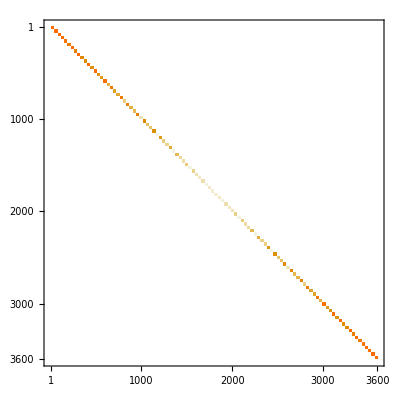

```mathematica
$H5DVR["PotentialEnergy"]//MatrixPlot
```

##### Grid PE

```mathematica
ListPlot3D[
$H5DVR["GridPotentialEnergy"]/.(1.*10^9->0),
RegionFunction->(h5RegMemFunc[{#, #2}]&),
ColorFunction->h5ColFun,
ColorFunctionScaling->False
]
```

-Graphics3D-

#### Ham

```mathematica
nwf=$H5DVR["Points"->{60, 60}, "NumberOfWavefunctions"->5];
```

```mathematica
nwf["Wavefunctions"]["Energies"]
```

{950.049,1603.41,1950.95,2519.21,2689.26}

```mathematica
#-#[[1]]&@nwf["Wavefunctions"]["Energies"]
```

{0.,653.363,1000.9,1569.16,1739.21}

##### Pruning Tests

```mathematica
ChemTools["Get", "DVR/Package/Object"]
ChemTools["Get", "DVR/Package/Defaults"]
```

Get::noopen: Cannot open /Users/Mark/Documents/Wolfram Mathematica/Applications/ChemTools/Packages/DVR/Package/Defaults.m.

$Failed

##### 120 Unpruned

```mathematica
AbsoluteTiming[
$H5DVR["Hamiltonian","Points"->{120, 120}]
]
```

{2.21247,SparseArray[<3441600>, {14400, 14400}]}

```mathematica
AbsoluteTiming[
$H5DVR["Energies","Points"->{120, 120}]
]
```

$Aborted

##### Pruning at 20% of the energy range (on the grid)

```mathematica
peVec=Diagonal@$H5DVR["PotentialEnergy","Points"->{120, 120}];
```

```mathematica
MinMax@DeleteCases[Normal@peVec, 1.*10^9]
```

{-68.4641,88773.9}

```mathematica
AbsoluteTiming[
Rest[#]-First[#]&@
$H5DVR["Energies",
"Points"->{120, 120},
 "PruningEnergy"->
Rescale[.2, {0, 1}, {-68.46412516618649,88773.86585779088}]
]
]
```

{3.70104,{532.733,866.282,1251.94,1480.7,1827.45,1878.65,2138.86,2290.64,2475.39,2654.15,2762.2,2919.12,2980.99,3009.83,3175.9,3213.33,3400.41,3509.69,3644.91,3827.36,3855.87,3948.89,4120.12,4276.36}}

```mathematica
AbsoluteTiming[
Rest[#]-First[#]&@
$H5DVR["Energies",
"Points"->{80, 80},
 "PruningEnergy"->
Rescale[.2, {0, 1}, {-68.46412516618649,88773.86585779088}]
]
]
```

{0.860435,{532.264,865.618,1250.84,1479.57,1825.77,1877.24,2136.98,2288.42,2473.16,2651.41,2759.65,2915.61,2978.02,3005.94,3172.19,3209.12,3395.78,3504.25,3639.59,3820.77,3849.37,3942.32,4112.8,4268.12}}

##### Just pruning the off-grid points

HOLY SHIT OF COURSE THIS IS JUST GERSCHGORIN’S THEOREM!

```mathematica
AbsoluteTiming[
Rest[#]-First[#]&@
$H5DVR["Energies","Points"->{60, 60}, "PruningEnergy"->Scaled[.99]]
]
```

{0.975846,{531.949,865.129,1250.02,1478.68,1824.47,1876.14,2135.52,2286.67,2471.36,2649.21,2757.57,2912.72,2975.55,3002.7,3169.02,3205.45,3391.66,3499.31,3634.73,3814.79,3843.44,3936.39,4106.,4260.31}}

#### Wavefunctions

##### Energies

```mathematica
h5Engs=$H5DVR["Energies"]
```

{929.141,1461.09,1794.27,2179.16,2407.83,2753.61,2805.28,3064.66,3215.81,3400.5,3578.35,3686.71,3841.86,3904.69,3931.84,4098.16,4134.59,4320.8,4428.45,4563.87,4743.93,4772.58,4865.53,5035.14,5189.45}

```mathematica
Rest[h5Engs]-First[h5Engs]
```

{531.949,865.129,1250.02,1478.68,1824.47,1876.14,2135.52,2286.66,2471.36,2649.21,2757.57,2912.71,2975.55,3002.7,3169.02,3205.45,3391.66,3499.31,3634.73,3814.79,3843.44,3936.39,4106.,4260.31}

##### Wavefunctions

```mathematica
h5Wfns=$H5DVR["Wavefunctions"];
```

### Based Off Anne’s Potential:

```mathematica
pot2=
Sort[
Import["~/Documents/UW/Research/H5+/archived/pot_cut.dat"][[All,
{2,1,3}
]]
];
potInterp2=
Interpolation[
QuantityMagnitude@
UnitConvert[
QuantityArray[pot2, {"BohrRadius", "BohrRadius", "Wavenumbers"}],
{"Angstroms", "Angstroms", "Wavenumbers"}
]
(*{
"ExtrapolationHandler"->
{(0.&),"WarningMessage"->False}
}*)
];
```

```mathematica
potInterp2["Domain"]
```

{{-2.47487,2.47487},{0.565686,4.24264}}

```mathematica
h5Stuff=
Quiet@
$H5DVR[
"PotentialFunction"->(potInterp2@@#&)
];
```

```mathematica
Export["~/Documents/UW/Research/H5+/results/hp_wfns_anne.mx", h5Stuff]
```

~/Documents/UW/Research/H5+/results/hp_wfns_anne.mx

```mathematica
h5Stuff["Wavefunctions"]["Energies"]
```

{928.326,1458.3,1790.23,2172.75,2400.85,2743.68,2797.15,3054.16,3202.77,3387.13,3561.96,3670.64,3817.39,3879.17,3903.33,4040.8,4058.1,4203.26,4259.28,4392.37,4498.04,4582.57,4731.33,4756.98,4833.45}

```mathematica
#-#[[1]]&@h5Stuff["Wavefunctions"]["Energies"]
```

{0.,529.976,861.902,1244.43,1472.52,1815.36,1868.82,2125.84,2274.45,2458.81,2633.63,2742.31,2889.06,2950.84,2975.,3112.47,3129.77,3274.93,3330.95,3464.04,3569.71,3654.24,3803.,3828.66,3905.12}

```mathematica
h5Stuff["Wavefunctions"]["Energies"]
```

{928.396,1458.35,1790.39,2172.92,2400.91,2743.65,2797.12,3054.02,3202.58,3386.97,3561.98,3670.69,3817.54,3879.22,3903.41,4039.,4055.37,4197.01,4250.1,4381.91,4482.97,4571.28,4719.77,4743.19,4821.46}